```mathematica
Euler-Lagrange equations;
Clear["Global`*"]
Needs["VariationalMethods`"];
 $Assumptions = {b > 0, m(a + b Cos[θ[t]]) > 0}; 
Π= m b g Sin[θ[t]];
T = m (b^2 θ'[t]^2+ ψ'[t]^2(a + b Cos[θ[t]])^2)/2;
L = T -Π
EL = EulerEquations[L,{θ[t],ψ[t] },t]{θ''[t], ψ''[t]}[[1]]//Simplify // MatrixForm
```

-b g m Sin[θ[t]]+1/2 m (b^2 θ'[t]^2+(a+b Cos[θ[t]])^2 ψ'[t]^2)

((g Cos[θ[t]]+(a+b Cos[θ[t]]) Sin[θ[t]] ψ'[t]^2+b θ''[t]==0) θ''[t]
(2 b Sin[θ[t]] θ'[t] ψ'[t]==(a+b Cos[θ[t]]) ψ''[t]) θ''[t])

```mathematica
Hamilton equations;
```

```mathematica
S1 = Solve[D[L,θ'[t]] == p1[t], θ'[t]][[1]]; (*!!!*)
S2 = Solve[D[L, ψ'[t]] == p2[t], ψ'[t]][[1]];(*!!!*)
H1 = θ'[t]p1[t] - L /.S1 //Simplify;
H2 = ψ'[t]p2[t] - L /.S2//Simplify;
Ham1 = {θ'[t] == D[H1,p1[t]], p1'[t] == -D[H1, θ[t]]};
Ham2 = { ψ'[t] == D[H2,p2[t]], p2'[t] == -D[H2, ψ[t]]};
{Ham1,Ham2 } 

T1 = Solve[Ham1[[2]], p1'[t]][[1]];
D[Ham1[[1]], t] /. T1 //Simplify

T2 = Solve[Ham2[[2]], p2'[t]][[1]];
D[Ham2[[1]], t] /. T2 //Simplify // MatrixForm
```

{{θ'[t]==p1[t]/(b^2 m),p1'[t]==1/2 m (-2 b g Cos[θ[t]]-2 b (a+b Cos[θ[t]]) Sin[θ[t]] ψ'[t]^2)},{ψ'[t]==p2[t]/(m (a+b Cos[θ[t]])^2),p2'[t]==0}}

g Cos[θ[t]]+(a+b Cos[θ[t]]) Sin[θ[t]] ψ'[t]^2+b θ''[t]==0

m (a+b Cos[θ[t]])^3 ψ''[t]==2 b p2[t] Sin[θ[t]] θ'[t]

```mathematica
First integrals;
```

```mathematica
FirstIntegrals[L,{θ[t],ψ[t]},t] //Apart // MatrixForm
```

(FirstIntegral[ψ]→-m (a+b Cos[θ[t]])^2 ψ'[t]
FirstIntegral[t]→1/2 b m (2 g Sin[θ[t]]+b θ'[t]^2)+1/2 m (a+b Cos[θ[t]])^2 ψ'[t]^2)

```mathematica
Routh equations;
```

```mathematica
D1 = Solve[D[L,ψ'[t]] == β[t],ψ'[t]][[1]] //Simplify;
betta = {β[t]-> p};

R = Simplify[L - ψ'[t]β[t] /.D1] /.betta
```

-p^2/(2 m (a+b Cos[θ[t]])^2)+1/2 b m (-2 g Sin[θ[t]]+b θ'[t]^2)

```mathematica
RouthEq=FullSimplify[EulerEquations[R, θ[t], t],Assumptions->{g>0,b>0, m>0, m(a + b Cos[θ[t]]) > 0}] /.betta
```

b g m Cos[θ[t]]+(b p^2 Sin[θ[t]])/(m (a+b Cos[θ[t]])^3)+b^2 m θ''[t]==0

```mathematica
Equilibrium States ;

EquilibriumStates  = Simplify[D[Π,θ[t] ] ==0, Assumptions->{g>0,b>0, m>0, m(a + b Cos[θ[t]]) > 0}];
Solve[EquilibriumStates,θ[t]] //TableForm
```

θ[t]→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]
θ[t]→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]

```mathematica
StationaryStates ;
```

```mathematica
StationaryStatesEquation = FullSimplify[D[-R,θ[t]] == 0,Assumptions-> {g > 0, m > 0, b > 0, m(a + b Cos[θ[t]]) > 0 }] /. betta
StationaryStates = Solve[StationaryStatesEquation , θ[t]] //Simplify // TableForm;
StationaryMotionEquation = RouthEq /.{θ[t]->γ,θ'[t]->0,θ''[t]->0};
SinGamma=Solve[StationaryMotionEquation,Sin[γ]][[1]]
```

g m^2 Cos[θ[t]] (a+b Cos[θ[t]])^3+p^2 Sin[θ[t]]==0

{Sin[γ]→-(g m^2 Cos[γ] (a+b Cos[γ])^3)/p^2}

```mathematica
Nonlinear equation;
```

```mathematica
AfterSubstitutionsR=R/.{θ[t]->γ+ξ[τ],θ'[t]->ω ξ'[τ],θ''[t]->ω^2 ξ''[τ]}
X={ξ[τ],ξ'[τ]};n=Length[X];
XiTo0=Table[X[[i]]->0,{i,1,n}];
```

-p^2/(2 m (a+b Cos[γ+ξ[τ]])^2)+1/2 b m (-2 g Sin[γ+ξ[τ]]+b ω^2 ξ'[τ]^2)

```mathematica
Linearaized equation;
```

```mathematica
Series2R=Sum[(D[AfterSubstitutionsR,X[[i]]]/.XiTo0)X[[i]],{i,1,n}]+1/2 Sum[(D[AfterSubstitutionsR,X[[i]],X[[j]]]/.XiTo0)X[[i]]X[[j]],{i,1,n},{j,1,n}] // Simplify;
V2=VariationalD[Series2R,ξ[τ],τ]//Simplify;
```

```mathematica
Almost linearaized equation;
```

```mathematica
Series4R =Sum[(D[AfterSubstitutionsR, X[[i]]] /. XiTo0) X[[i]], {i, 1, n}] + 1/2 Sum[(D[AfterSubstitutionsR, X[[i]], X[[j]]] /. XiTo0) X[[i]] X[[j]], {i, 1, n}, {j, 1, n}] +
   1/6 Sum[(D[AfterSubstitutionsR, X[[i]], X[[j]], X[[k]]] /. XiTo0) X[[i]] X[[j]] X[[k]], {i, 1, n}, {j, 1, n}, {k, 1, n}] +
   1/24 Sum[(D[AfterSubstitutionsR, X[[i]], X[[j]], X[[k]], X[[l]]] /. XiTo0) X[[i]] X[[j]] X[[k]] X[[l]], {i, 1, n}, {j, 1, n}, {k, 1, n}, {l, 1, n}] //Simplify;

V4=VariationalD[Series4R,ξ[τ],τ]//Simplify;
```

```mathematica
Nondimensionalization of linearaized equation;
```

```mathematica
TransformedLinEq=EulerEquations[Series2R,ξ[τ],τ][[1]] /. SinGamma //Simplify 
SubstitutionForP={ p->m (a+b Cos[γ])^2 ω0 };
NonDimRules={a->b α, g->G b ω0^2, ω->ω0};
NonDimLinEq=TransformedLinEq/(b^2*m*ω0^2)/.SubstitutionForP/.NonDimRules//Simplify;
ExpressionForG=Solve[(StationaryMotionEquation/.SubstitutionForP/.NonDimRules//Simplify),G][[1]];
NonDimLinEq = NonDimLinEq/.ExpressionForG//Simplify
```

-(b p^2 Cos[γ] ξ[τ])/(m (a+b Cos[γ])^3)-(b g^2 m^3 Cos[γ] (a+b Cos[γ])^2 (a+4 b Cos[γ]) ξ[τ])/p^2-b^2 m ω^2 ξ''[τ]

-1/4 (7+(4 α-3 Cos[3 γ]) Sec[γ]) ξ[τ]-ξ''[τ]

```mathematica
Nondimensionalization of almost linearaized equation;
```

```mathematica
TransformedALEq=EulerEquations[Series4R,ξ[τ],τ][[1]] /. SinGamma //Simplify;
NonDimALeq=TransformedALEq/(b^2*m*ω0^2)/.SubstitutionForP/.NonDimRules//Simplify;
NonDimALeq/.ExpressionForG//Simplify
```

-1/(96 (α+Cos[γ])^2)Sec[γ] (24 (α+Cos[γ])^2 (4 α+7 Cos[γ]-3 Cos[3 γ]) ξ[τ]+18 (20 α+(13+12 α^2) Cos[γ]+4 α Cos[2 γ]-Cos[3 γ]) Sin[2 γ] ξ[τ]^2+(180 α-16 α^3+6 (53+2 α^2) Cos[γ]+120 α Cos[2 γ]-199 Cos[3 γ]+84 α^2 Cos[3 γ]-60 α Cos[4 γ]+9 Cos[5 γ]) ξ[τ]^3+96 Cos[γ] (α+Cos[γ])^2 ξ''[τ])

```mathematica
Nondimensionalization of nonlinear equation;
```

```mathematica
TransformedNonLinEq=EulerEquations[AfterSubstitutionsR,ξ[τ],τ][[1]] /. SinGamma //Simplify ;
NonDimNonLinEq=TransformedNonLinEq/(b^2*m*ω0^2)/.SubstitutionForP/.NonDimRules//Simplify;
NonDimNonLinEq/.ExpressionForG//Simplify
```

-((α+Cos[γ])^4 Sin[γ+ξ[τ]])/(α+Cos[γ+ξ[τ]])^3+(α+Cos[γ]) Cos[γ+ξ[τ]] Tan[γ]-ξ''[τ]

```mathematica
Characteristic equation for non-dimensional linear equation;
```

```mathematica
CharacteristicEq = Coefficient[NonDimLinEq, ξ''[τ]] λ^2  +  Coefficient[NonDimLinEq, ξ'[τ]]λ +  Coefficient[NonDimLinEq, ξ[τ]]==0
```

-λ^2+1/4 (-7-(4 α-3 Cos[3 γ]) Sec[γ])==0

```mathematica
Eigenvalues for characteristic equation;
```

```mathematica
exp=Table[(D[ξ[τ],{τ,i}]->ⅇ^(λ τ)λ^i),{i,0,2}];
(NonDimLinEq==0)/.exp;
EigenValue = λ /. Solve[% , λ]  
Transpose[{Re[%],Im[%]}];
Manipulate[ListPlot[%,PlotRange->{{-10,10},{-10,10}}],{α,0,5},{γ,-π,π}]
```

{-1/2 √(-7-4 α Sec[γ]+3 Cos[3 γ] Sec[γ]),1/2 √(-7-4 α Sec[γ]+3 Cos[3 γ] Sec[γ])}

```mathematica
Transform equation to the first order system;
```

```mathematica
X = {Subscript[x, 1][τ], Subscript[x, 2][τ]};
X' = D[X, τ];
System = {Subscript[x, 2]'[τ] == Coefficient[NonDimLinEq, ξ[τ]] Subscript[x, 1][τ], Subscript[x, 1]'[τ] == Subscript[x, 2][τ]};
F= X' /. First@Solve[System , X'];
A = Table[D[F[[i]], X[[j]]], {i, 1, 2}, {j, 1, 2}];
X' == A.X // Thread //MatrixForm
EigenvaluesA = Eigenvalues[A] // Thread // TableForm;
EigenvectorsA = Eigenvectors[A] //MatrixForm;
```

(x_1'[τ]==x_2[τ]
x_2'[τ]==1/4 (-7-4 α Sec[γ]+3 Cos[3 γ] Sec[γ]) x_1[τ])

```mathematica
Hurwitz matrix;
```

```mathematica
Sum[λ^(2-i) a[i], {i, 0, 2}] == 0;
B= Table[If[0 ≤ 2 j - i ≤ 2, a[2j-i], 0], {i, 0, 2}, {j, 0, 2}] 
B // MatrixForm
F = Table[Det[B[[1;; i, 1;; i]]] > 0, {i, 1, 2}]
FF=Table[a[i] > 0, {i, 0, 2}]
```

{{a[0],a[2],0},{0,a[1],0},{0,a[0],a[2]}}

(a[0] | a[2] | 0
0 | a[1] | 0
0 | a[0] | a[2])

{a[0]>0,a[0] a[1]>0}

{a[0]>0,a[1]>0,a[2]>0}

```mathematica
Hurwitz inequalities;
```

```mathematica
Cond = {a[0]->-1,a[1]->0,a[2]->-1/4 (-7-(4 α-3 Cos[3 γ]) Sec[γ])};
a[2]>0; 
HurwititzIneq=FullSimplify[%/.Cond ]&&α>1
```

5+2 α Sec[γ]>3 Cos[2 γ]&&α>1

```mathematica
Stability domain;
```

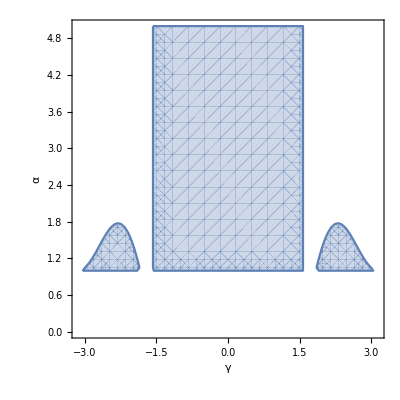

```mathematica
StabilityDomain = RegionPlot[Evaluate[HurwititzIneq ], {γ, -π, π}, {α, 0, 5},  AxesLabel -> {"γ", "α"}]
```

```mathematica
Crossing the borders;
```

```mathematica
Eq[g_, a_] := {Evaluate[NonDimLinEq /. {γ -> g} /. {α -> a }] == 0};
BoundCond = {ξ[0] == 1, ξ'[0] == 1};
Φ[γ_,α_, τ_] := ξ[τ] /. First@DSolve[Flatten[Union[Eq[γ, α], BoundCond]], ξ[τ], τ];
MotionType = Manipulate[Plot[Evaluate[Φ[γ,α, τ]], {τ, 0, 20}, PlotRange->{{0,20},{-20, 20}}], {γ, -π, π, 0.01 , Appearance -> "Open"}, {α,0, 5,0.01, Appearance -> "Open" }]
```

```mathematica
Assignment 5a;
```

```mathematica
A1 = {{0, 1, 1, 1}, {-1, 0, 1,1}, {0,0,0,1}, {0, 0, -1, 0}};
```

```mathematica
A1 // MatrixForm
```

(0 | 1 | 1 | 1
-1 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
EigenValuesA1 = Eigenvalues[A1]
```

{ⅈ,ⅈ,-ⅈ,-ⅈ}

```mathematica
EigenVectorsA1 = Eigenvectors[A1]
```

{{-ⅈ,1,0,0},{0,0,0,0},{ⅈ,1,0,0},{0,0,0,0}}

```mathematica
DiagonalizableMatrixQ[A1]
```

False

```mathematica
JordanForm = JordanDecomposition[A1][[2]]
```

{{-ⅈ,1,0,0},{0,-ⅈ,0,0},{0,0,ⅈ,1},{0,0,0,ⅈ}}

```mathematica
JordanForm // MatrixForm
```

(-ⅈ | 1 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 1
0 | 0 | 0 | ⅈ)

```mathematica
n  = Length[A1];
```

```mathematica
m = Length[JordanForm];
```

```mathematica
X = Table[x[i][t], {i, 1, n}]
```

{x[1][t],x[2][t],x[3][t],x[4][t]}

```mathematica
X' = D[X, t]
```

{x[1]'[t],x[2]'[t],x[3]'[t],x[4]'[t]}

```mathematica
F= Thread[X' == A1.X]
```

{x[1]'[t]==x[2][t]+x[3][t]+x[4][t],x[2]'[t]==-x[1][t]+x[3][t]+x[4][t],x[3]'[t]==x[4][t],x[4]'[t]==-x[3][t]}

```mathematica
InitialCondition = Table[x[i][0] == 1, {i, 1, n}]
```

{x[1][0]==1,x[2][0]==1,x[3][0]==1,x[4][0]==1}

```mathematica
Solution = X /. First@DSolve[Union[F, InitialCondition], X, t]
```

{Cos[t]+t Cos[t]+2 Sin[t]+t Sin[t],Cos[t]+t Cos[t]-t Sin[t],Cos[t]+Sin[t],Cos[t]-Sin[t]}

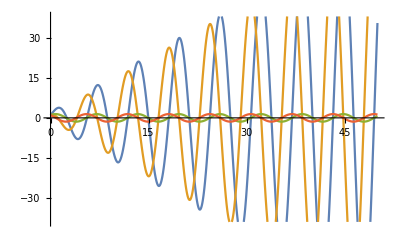

```mathematica
Plot[Solution, {t, 0, 50}]
```

```mathematica
Research of stability;
```

```mathematica
JordanMatrix = {{-ⅈ,1,0,0,0},{0,-ⅈ,0,0,0},{0,0,ⅈ,1,0},{0,0,0,ⅈ,0}};
```

```mathematica
temp = 0;
For[i=1,i<m + 1,i++,If[(Re[JordanMatrix[[i,i]]] == 0 && JordanMatrix[[i,i+1]] == 0)|| Re[JordanMatrix[[i,i]]] < 0, temp = temp +0, temp = temp +1]];
If[temp== 0, Print["System is Stable"], Print["System is Unstable"]]
```

System is Unstable

```mathematica
Assignment 7;
```

```mathematica
A = {{-1, Sin[t], 0}, {Cos[t], -a, -Sin[t]}, {0, Cos[t], a}};
```

```mathematica
Y[t_] = {y[1][t],y[2][t],y[3][t]};
```

```mathematica
SystemWithPeriodicCoefficients = Thread[D[Y[t], t] == A.Y[t]];
```

```mathematica
IdentrityMatrix= {{y[1][0]==1,y[2][0]==0,y[3][0]==0},{y[1][0]==0,y[2][0]==1,y[3][0]==0},{y[1][0]==0,y[2][0]==0,y[3][0]==1}};
```

```mathematica
SystemSolution[b_] := Table[Y[t] /. First[NDSolve[Union[SystemWithPeriodicCoefficients /. {a -> b}, IdentrityMatrix[[i]]], Y[t], {t, 0, 2 π}]], {i, 3}]
```

```mathematica
MaxAbs[b_] := Max[Abs[Eigenvalues[SystemSolution[b] /. {t -> 2 π}]]]
```

```mathematica
a1 = -1;
```

```mathematica
While[Abs[MaxAbs[a1]-1] > 0.001 && a1 < 0, a1 = a1 + 0.0001]
```

```mathematica
a2 = a1 + 0.01;
```

```mathematica
While[Abs[MaxAbs[a2]-1] > 0.001 && a2 < 0, a2 = a2 + 0.0001]
```

```mathematica
EigenValue1 = Eigenvalues[SystemSolution[a1] /. {t -> 2 π}];
```

```mathematica
EigenValue2 = Eigenvalues[SystemSolution[a2] /. {t -> 2 π}];
```

```mathematica
λ = {EigenValue1,EigenValue2 } // TableForm
```

1.00007+0. ⅈ | 0.0129157+0.041237 ⅈ | 0.0129157-0.041237 ⅈ
1.00008 | 0.0619868 | 0.0301242

```mathematica
StringForm["Zero Solution is Stable for: `` < a < ``", NumberForm[a1, {3, 3}], NumberForm[a2, {3, 3}]]
```

Zero Solution is Stable for: -0.611 < a < -0.433

```mathematica
Manipulate[{Plot[Evaluate[#], {t, 0, 2 π}] &/@ Transpose[SystemSolution[a]]} // TableForm, {a, -0.611, -0.433, 0.001, Appearance->"Open"}]
```